## Importing the ^163 Lu data from CXX output

## Graphical representation for the excitation energies and contour plots for all the approaches used in novel formalism

```mathematica
approachA1=Import["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Data/Unified_Model/fitA1_cxx.dat"];
approachA2=Import["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Data/Unified_Model/fitA2_cxx.dat"];
approachB1=Import["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Data/Unified_Model/fitB1_cxx.dat"];
approachB2=Import["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Data/Unified_Model/fitB2_cxx.dat"];
```

## Storing the fit parameters

```mathematica
paramsA1=approachA1[[1]];
paramsA2=approachA2[[1]];
paramsB1=approachB1[[1]];
paramsB2=approachB2[[1]];
```

## Storing the spins for each state (same across approaches)

```mathematica
spin1=Table[approachA1[[i,1]],{i,2,22}];
spin2=Table[approachA1[[i,1]],{i,23,39}];
spin3=Table[approachA1[[i,1]],{i,40,53}];
spin4=Table[approachA1[[i,1]],{i,54,63}];
```

## Storing the excitation energies for each approach

### APPROACH A1

```mathematica
tsd1ExpA1=Table[approachA1[[i,2]],{i,2,22}];
tsd1ThA1=Table[approachA1[[i,3]],{i,2,22}];
tsd2ExpA1=Table[approachA1[[i,2]],{i,23,39}];
tsd2ThA1=Table[approachA1[[i,3]],{i,23,39}];
tsd3ExpA1=Table[approachA1[[i,2]],{i,40,53}];
tsd3ThA1=Table[approachA1[[i,3]],{i,40,53}];
tsd4ExpA1=Table[approachA1[[i,2]],{i,54,63}];
tsd4ThA1=Table[approachA1[[i,3]],{i,54,63}];
```

### APPROACH A2

```mathematica
tsd1ExpA2=Table[approachA2[[i,2]],{i,2,22}];
tsd1ThA2=Table[approachA2[[i,3]],{i,2,22}];
tsd2ExpA2=Table[approachA2[[i,2]],{i,23,39}];
tsd2ThA2=Table[approachA2[[i,3]],{i,23,39}];
tsd3ExpA2=Table[approachA2[[i,2]],{i,40,53}];
tsd3ThA2=Table[approachA2[[i,3]],{i,40,53}];
tsd4ExpA2=Table[approachA2[[i,2]],{i,54,63}];
tsd4ThA2=Table[approachA2[[i,3]],{i,54,63}];
```

### APPROACH B1

```mathematica
tsd1ExpB1=Table[approachB1[[i,2]],{i,2,22}];
tsd1ThB1=Table[approachB1[[i,3]],{i,2,22}];
tsd2ExpB1=Table[approachB1[[i,2]],{i,23,39}];
tsd2ThB1=Table[approachB1[[i,3]],{i,23,39}];
tsd3ExpB1=Table[approachB1[[i,2]],{i,40,53}];
tsd3ThB1=Table[approachB1[[i,3]],{i,40,53}];
tsd4ExpB1=Table[approachB1[[i,2]],{i,54,63}];
tsd4ThB1=Table[approachB1[[i,3]],{i,54,63}];
```

### APPROACH B2

```mathematica
tsd1ExpB2=Table[approachB2[[i,2]],{i,2,22}];
tsd1ThB2=Table[approachB2[[i,3]],{i,2,22}];
tsd2ExpB2=Table[approachB2[[i,2]],{i,23,39}];
tsd2ThB2=Table[approachB2[[i,3]],{i,23,39}];
tsd3ExpB2=Table[approachB2[[i,2]],{i,40,53}];
tsd3ThB2=Table[approachB2[[i,3]],{i,40,53}];
tsd4ExpB2=Table[approachB2[[i,2]],{i,54,63}];
tsd4ThB2=Table[approachB2[[i,3]],{i,54,63}];
```

## Function for creating a list-plot for exp vs. theory

```mathematica
energyPlot[spin_,exp_,th_,text_]:=ListPlot[{Table[{spin[[i]],exp[[i]]},{i,1,Length[spin]}],Table[{spin[[i]],th[[i]]},{i,1,Length[spin]}]},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],Joined->{False,True},PlotStyle->{{Red,Thick},{Black,Thick}},ImageSize->Medium,PlotMarkers->{{Automatic,9},None},AspectRatio->0.75,FrameLabel->{"I [ℏ]","E [MeV]"},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},PlotLegends->Placed[{"Exp","Th."},{0.80,0.2}],Epilog->Inset[Style[StringTemplate["``"][text],20,Black,Bold,FontFamily->"Times New Roman",Italic],Scaled[{0.2,0.80}]]];
```

## Creating the plots for each approach

## A1

```mathematica
p1A1=energyPlot[spin1,tsd1ExpA1,tsd1ThA1,"TSD1"];
p2A1=energyPlot[spin2,tsd2ExpA1,tsd2ThA1,"TSD2"];
p3A1=energyPlot[spin3,tsd3ExpA1,tsd3ThA1,"TSD3"];
p4A1=energyPlot[spin4,tsd4ExpA1,tsd4ThA1,"TSD4"];
```

## A2

```mathematica
p1A2=energyPlot[spin1,tsd1ExpA2,tsd1ThA2,"TSD1"];
p2A2=energyPlot[spin2,tsd2ExpA2,tsd2ThA2,"TSD2"];
p3A2=energyPlot[spin3,tsd3ExpA2,tsd3ThA2,"TSD3"];
p4A2=energyPlot[spin4,tsd4ExpA2,tsd4ThA2,"TSD4"];
```

## B1

```mathematica
p1B1=energyPlot[spin1,tsd1ExpB1,tsd1ThB1,"TSD1"];
p2B1=energyPlot[spin2,tsd2ExpB1,tsd2ThB1,"TSD2"];
p3B1=energyPlot[spin3,tsd3ExpB1,tsd3ThB1,"TSD3"];
p4B1=energyPlot[spin4,tsd4ExpB1,tsd4ThB1,"TSD4"];
```

## B2

```mathematica
p1B2=energyPlot[spin1,tsd1ExpB2,tsd1ThB2,"TSD1"];
p2B2=energyPlot[spin2,tsd2ExpB2,tsd2ThB2,"TSD2"];
p3B2=energyPlot[spin3,tsd3ExpB2,tsd3ThB2,"TSD3"];
p4B2=energyPlot[spin4,tsd4ExpB2,tsd4ThB2,"TSD4"];
```

## Function for creating a grid plot

```mathematica
gridplot[p1_,p2_,p3_,p4_]:=GraphicsGrid[{{p1,p2},{p3,p4}},ImageSize->Large,Frame->All];
```

## The excitation energies in each approach

## A1

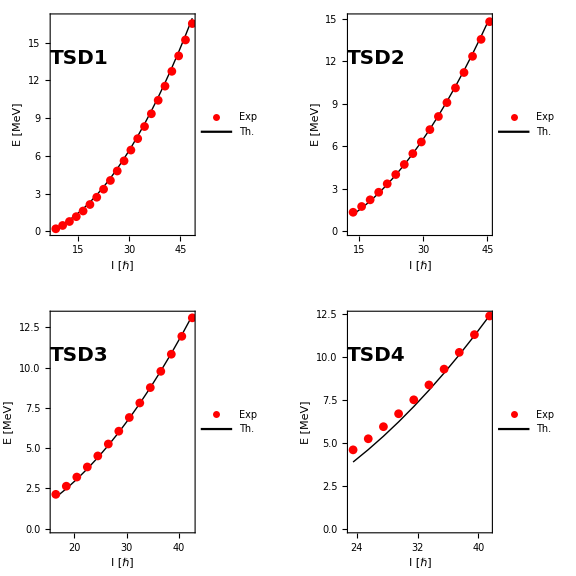

```mathematica
Show[gridplot[p1A1,p2A1,p3A1,p4A1]]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/Unified_Model/Energies_formalism_A1.png",Show[gridplot[p1A1,p2A1,p3A1,p4A1]]];
```

## A2

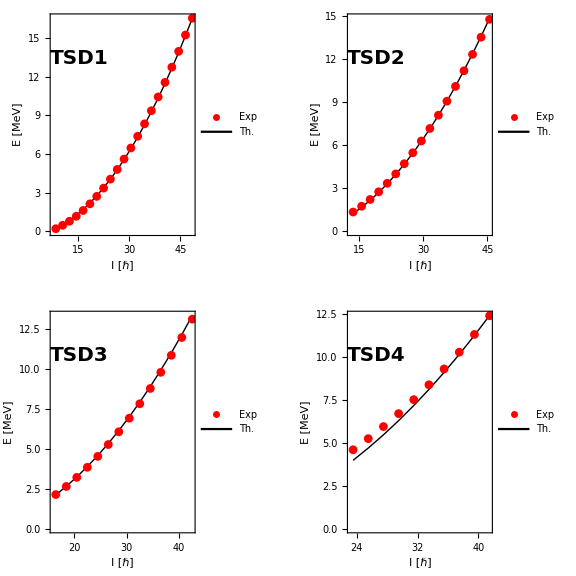

```mathematica
Show[gridplot[p1A2,p2A2,p3A2,p4A2]]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/Unified_Model/Energies_formalism_A2.png",Show[gridplot[p1A2,p2A2,p3A2,p4A2]]];
```

## B1

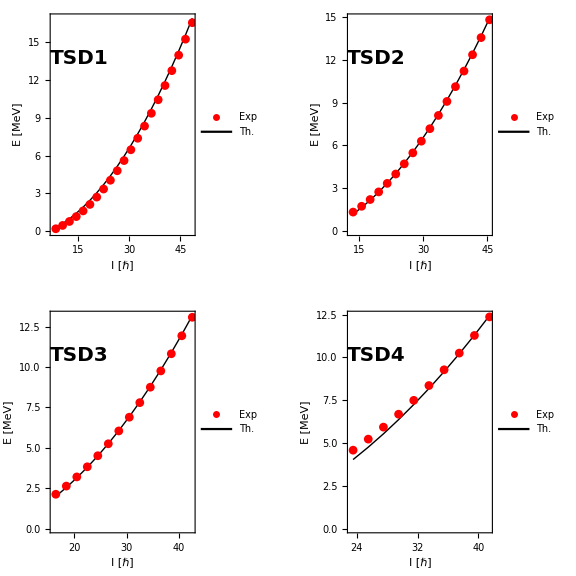

```mathematica
Show[gridplot[p1B1,p2B1,p3B1,p4B1]]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/Unified_Model/Energies_formalism_B1.png",Show[gridplot[p1B1,p2B1,p3B1,p4B1]]];
```

## B2

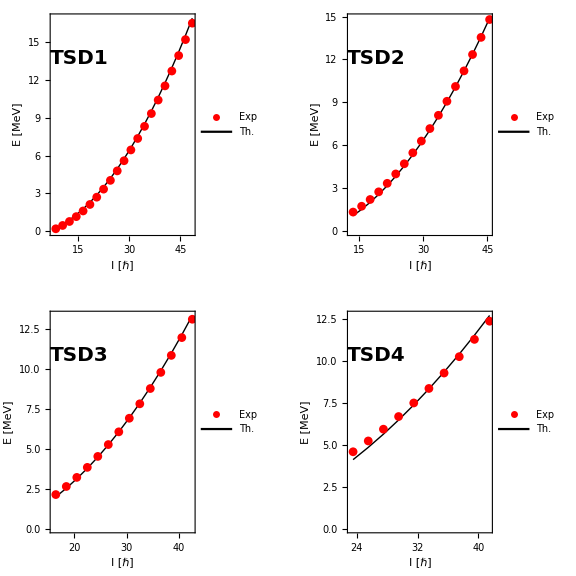

```mathematica
Show[gridplot[p1B2,p2B2,p3B2,p4B2]]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/Unified_Model/Energies_formalism_B2.png",Show[gridplot[p1B2,p2B2,p3B2,p4B2]]];
```